# T-Model(m=1) Model

# This notebook is a part of my Diploma Thesis with title “Swampland Conjectures and Constraints on Inflation” . The knowledge of the theoretical results is important, if someone wishes to follow the presented results in this notebook. My Thesis can be found in an other file in my GitHub repository.

## Definition of the Potential and Introduction of the Slow-Roll parameters

## In this section we will introduce the potential and the slow-roll parameters

```mathematica
v[x_]:=Λ^4*(Tanh[x/((√(6*w))/k)])^2
ε1=a/(2*k^2)*(v'[x]/v[x])^2// Simplify;
ε2=-a/k^2*(v''[x]/v[x])+ε1// Simplify;
ε=ε1/a// Simplify;
η=1/k^2*(v''[x]/v[x])// Simplify;
η1=a*η// Simplify;
```

It is required by the theory that the period of inflation should stop when the flatness conditions are a not satisfied, so when ε1=1

```mathematica
Solve[ε1==1,x]
```

{{x→ConditionalExpression[(√(3/2) √w (-ArcSinh[(2 √a)/(√3 √w)]+2 ⅈ π C[1]))/k, C[1]∈ℤ]},{x→ConditionalExpression[(√(3/2) √w (ⅈ π-ArcSinh[(2 √a)/(√3 √w)]+2 ⅈ π C[1]))/k, C[1]∈ℤ]},{x→ConditionalExpression[(√(3/2) √w (ArcSinh[(2 √a)/(√3 √w)]+2 ⅈ π C[1]))/k, C[1]∈ℤ]},{x→ConditionalExpression[(√(3/2) √w (ⅈ π+ArcSinh[(2 √a)/(√3 √w)]+2 ⅈ π C[1]))/k, C[1]∈ℤ]}}

We have to choose second possible solution, so we set with xf the final value for the φ.

```mathematica
xf=(√(3/2) √w (ArcSinh[(2 √a)/(√3 √w)]))/k// Simplify
```

(√(3/2) √w ArcSinh[(2 √a)/(√3 √w)])/k

We proceed to the calculation of the initial value of φ , which denoted as xi
Firstly, the integral for the e-folding number is calculated.

```mathematica
Integrate[-(k^2/a)*(v[x]/v'[x]),x]
```

-(3 w Cosh[(√(2/3) k x)/(√w)])/(4 a)

```mathematica
Solve[-(3 w Cosh[(√(2/3) k xf)/(√w)])/(4 a)-(-(3 w Cosh[(√(2/3) k x)/(√w)])/(4 a))==Y,x]
```

{{x→ConditionalExpression[(√(3/2) √w (-ArcCosh[(3 √(1+(4 a)/(3 w)) w+4 a Y)/(3 w)]+2 ⅈ π C[1]))/k, C[1]∈ℤ]},{x→ConditionalExpression[(√(3/2) √w (ArcCosh[(3 √(1+(4 a)/(3 w)) w+4 a Y)/(3 w)]+2 ⅈ π C[1]))/k, C[1]∈ℤ]}}

```mathematica
xi=√(3/2) √w (ArcCosh[(3 √(1+(4 a)/(3 w)) w+4 a Y)/(3 w)])// Simplify
```

√(3/2) √w ArcCosh[(√(9+(12 a)/w) w+4 a Y)/(3 w)]

# Calculation of the observational indices

We calculate the slow-roll parameters for
φ = φi and we take the Taylor approximation for N → ∞. Afterwards, we
calculate the primordial density perturbation and the tensor to scalar ratio for φ = φi and we start our primary work.

```mathematica
ε1i=ε1 /. x->xi// Simplify;
ε2i=ε2 /. x->xi// Simplify;
εi=ε /. x->xi// Simplify;
η1i=η1 /. x->xi// Simplify;
ηi=η/. x->xi// Simplify;
```

```mathematica
ε1i60=ε1i/. Y->60// Simplify;
ε2i60=ε2i/.Y->60// Simplify;
εi60=εi/.Y->60// Simplify;
ηi60=ηi/.Y->60// Simplify;
η1i60=η1i/. Y->60// Simplify;
```

For these specific observational indices there is no need for Taylor approximation because no results can be obtained. So, we proceed with the primordial density perturbation and the tensor to scalar ratio:

```mathematica
ns=1-6*ε1i+2*η1i// Simplify;
ns60=ns/. Y->60//Simplify
r=16*ε1i// Simplify;
r60=r/. Y->60// Simplify
```

((-8 a-3 w+3 w Cosh[k ArcCosh[√(1+(4 a)/(3 w))+(80 a)/w]]) Csch[1/2 k ArcCosh[√(1+(4 a)/(3 w))+(80 a)/w]]^2)/(6 w)

(64 a Csch[k ArcCosh[√(1+(4 a)/(3 w))+(80 a)/w]]^2)/(3 w)

At this point we will set k=1 and the we calculate the required contour plots.

```mathematica
r60k=r60/. k->1//Simplify;
ns60k=ns60/. k->1// Simplify;
```

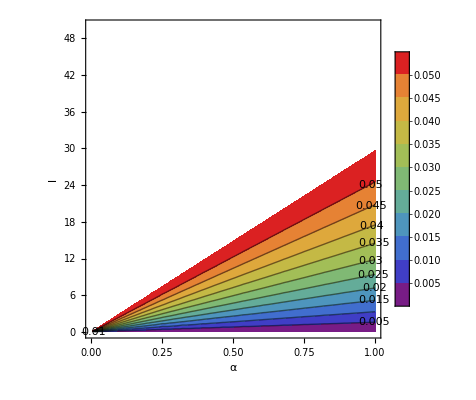

```mathematica
ContourPlot[r60k,{a,0,1},{w,10^(-2),50},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"},Contours->10,PlotRange->{0,0.056}]
```

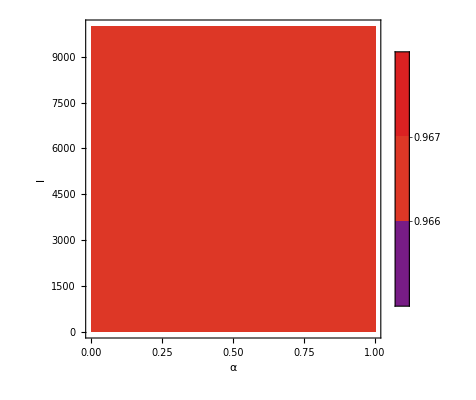

```mathematica
ContourPlot[ns60k,{a,0,1},{w,10^(-2),10^4},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"},PlotRange->{0.9607,0.9691}]
```

Slow- Roll parameters for N=60 and k=1.

```mathematica
ε1i60k=ε1i60/.k->1// Simplify;
ε2i60k=ε2i60/.k->1// Simplify;
εi60k=εi60/.k->1// Simplify;
ηi60k=ηi60/.k->1// Simplify;
η1i60k=η1i60/. k->1// Simplify;
```

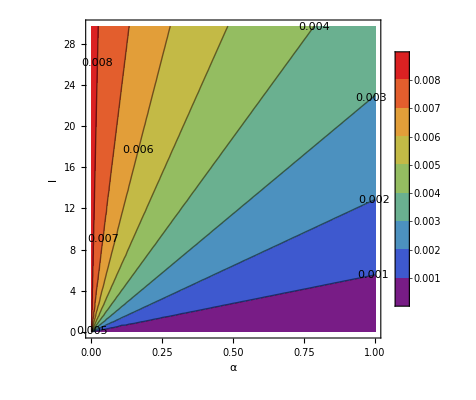

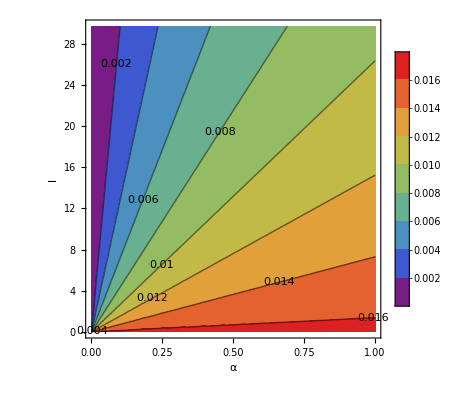

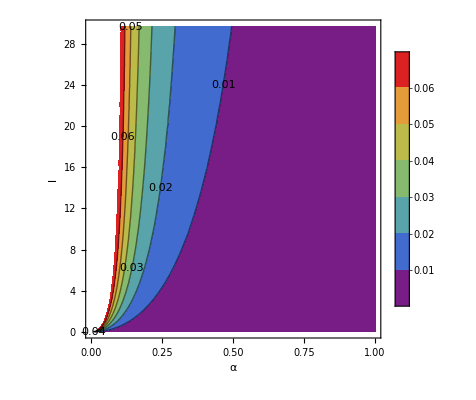

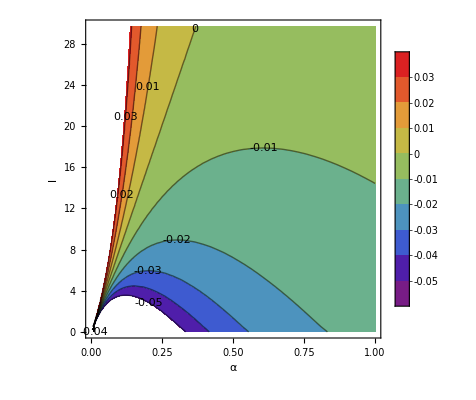

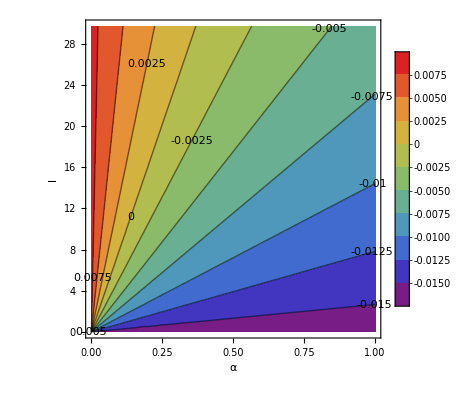

```mathematica
ContourPlot[ε1i60k,{a,0,1},{w,10^(-2),29.7},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"}]
ContourPlot[ε2i60k,{a,0,1},{w,10^(-2),29.7},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"}]
ContourPlot[εi60k,{a,0,1},{w,10^(-2),29.7},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"}]
ContourPlot[ηi60k,{a,0,1},{w,10^(-2),29.7},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"}]
ContourPlot[η1i60k,{a,0,1},{w,10^(-2),29.7},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"}]
```

## Swampland Conjectures

• The Swampland Distance Conjecture limits the validity of an E.F.T.
and set an upper limit for the traversable by the scalar field as following

                                  ∆φ ≤ f ∼ O(1), in natural units

• The De Sitter Conjecture. It declares that it is impossible to create
De Sitter vacua in string theory. This leads us to set of a lower limit
for the gradient of scalar potentials [Tri20]:
V’/V≥ g ∼ O(1). 
• Another important result is the following -V”/V≥ g ∼ O(1).

```mathematica
s1=v'[x]/v[x]// Simplify;
s1initial=s1/. x->xi// Simplify;
s1initial60=s1initial/. Y->60//Simplify;
s1initial60k=s1initial60 /.k->1// Simplify
```

(2 √6 √w)/(√((240 a-3 w+√(9+(12 a)/w) w)/(240 a+3 w+√(9+(12 a)/w) w)) (240 a+3 w+√(9+(12 a)/w) w))

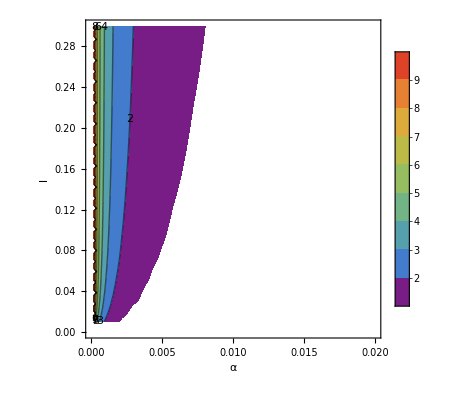

```mathematica
ContourPlot[s1initial60k,{a,0,.02},{w,10^(-2),0.3},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"},PlotRange->{1,10}]
```

(240 a-6 w+√(9+(12 a)/w) w)/(3 a (4800 a+w+40 √(9+(12 a)/w) w))

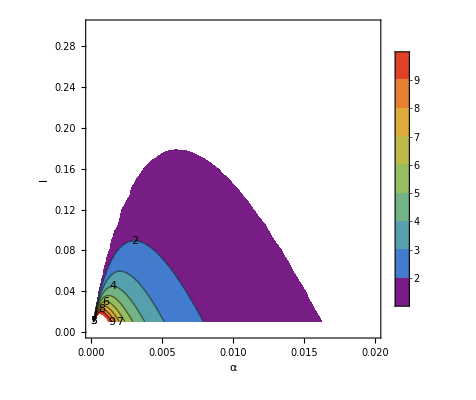

```mathematica
s=-v''[x]/v[x]// Simplify;
sinitial=s/. x->xi// Simplify;
sinitial60=sinitial/. Y->60//Simplify;
sinitial60k=sinitial60 /.k->1// Simplify

ContourPlot[sinitial60k,{a,0,.02},{w,10^(-2),0.3},ContourLabels->True,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"α","l"},PlotRange->{1,10}]
```